```mathematica
points={{17.5,2.82},{30,2.3},{40,2.02},{50,1.825},{60,1.7},{70,1.59},{80,1.5},{90,1.425},{100,1.41},{110,1.4}};
```

```mathematica
parabola = Fit[points, {1,x,x^2,x^3,x^4}, x]
```

4.0704-0.0940983 x+0.00149667 x^2-0.0000121924 x^3+3.963×10^-8 x^4

```mathematica
f[x_]=parabola
```

4.0704-0.0940983 x+0.00149667 x^2-0.0000121924 x^3+3.963×10^-8 x^4

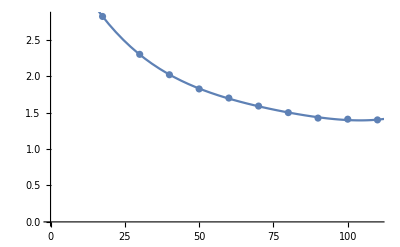

```mathematica
Show[ListPlot[points],Plot[parabola,{x,0,120}]]
```